## Importing the data

```mathematica
(*F=Import["/home/cnewby/SeniorDesign/Rbpots.dat"];
F=Import["/Users/jamcneil/Projects/RbRb/Potentials/Rbpots.dat"];
len=Length[F];*)
```

```mathematica
(*x=1;
A={};
B={};
While[x≤len,{AppendTo[A,{F⟦x,2⟧}],AppendTo[B,{F⟦x,3⟧}],x++}]*)
```

```mathematica
(*Vs=Array[1,{len,2}];
Vt=Array[1,{len,2}];
x=1;
While[x<len,{Vs⟦x,1⟧=x*.0003,Vs⟦x,2⟧=A⟦x,1⟧,Vt⟦x,1⟧=x*.0003,Vt⟦x,2⟧=B⟦x,1⟧,x++}]*)
```

```mathematica
ℏc=197.3269631;

αfsc=1/137.035999070;
a0=5.2917720859*10^-2;

Hartree=(αfsc*ℏc)/a0;Hartree=1;

potFile="/home/cnewby/SeniorDesign/Stuff/Rbpots.dat";
potList=ReadList[potFile,{Number,Number,Number}];
Np=Length[potList];len=Np;
rList=Table[potList[[i,1]],{i,1,Np}];
VsList=Table[potList[[i,2]],{i,1,Np}];VtList=Table[potList[[i,3]],{i,1,Np}];
VsDataList=Table[{rList[[i]],VsList[[i]]*Hartree},{i,1,Np}];
VtDataList=Table[{rList[[i]],VtList[[i]]*Hartree},{i,1,Np}];Vt=VtDataList;
VsPlot=ListPlot[VsDataList,Joined->True,PlotStyle->Blue,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VtPlot=ListPlot[VtDataList,Joined->True,PlotStyle->Red,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
```

```mathematica
Aa=ListPlot[{{.65,-.3}},PlotMarkers->"V_s"];
Bb=ListPlot[{{.49,.14}},PlotMarkers->"V_t",PlotStyle->Red];

Graph=Show[{VsPlot,VtPlot,Aa,Bb},PlotLabel->"Rubidium Potentials",AxesLabel->{"r (nm)","V(r) (eV)"},PlotRange->{{0,1},{-1,1}}]
```

-Graphics-

```mathematica
Export["/home/cnewby/Desktop/csm-thesis/Figures/Josepotentialplot.pdf",Graph]
```

/home/cnewby/Desktop/csm-thesis/Figures/Josepotentialplot.pdf

## Numerov Matching Method

## Numerov

```mathematica
Numerov[Vi_,E_,Ui_,Vim_,Uim_,Vip_]:=((2-5/6 h^2((-2μ)/ℏ^2(Vi-E)))Ui-(1+h^2/12((-2μ)/ℏ^2(Vim-E)))Uim)/(1+h^2/12((-2μ)/ℏ^2(Vip-E)));
```

## Constants

```mathematica
Clear[x,A,B];

h=rList[[3]]-rList[[2]];
m=84.911789738×931.494028×10^6;
μ=m/2;
ℏ=197.3269631;
EnList={};
state=1;
Vtmin=Min[Vt]
```

-0.0253217

```mathematica
(*min of Vt*)
imin=1;
While[imin<len,{If[Vt⟦imin,2⟧==Vtmin,{min=imin},1],imin++}]
```

```mathematica
min
StartPoint=.2;
istart=Floor[StartPoint/h]
```

1235

400

## Step

```mathematica
(*Initial Guess
guess=Vtmin+10^-4(*.0246149*);
guess=-.02(*.0246149*);
AppendTo[EnList,guess];
En=EnList⟦state⟧;
*)
```

-0.00335037

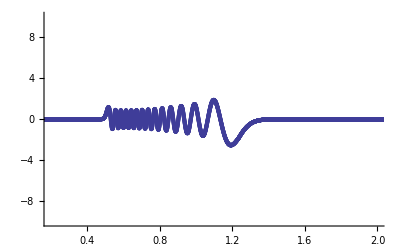

```mathematica
(*Answers*)
En=-.001;

(*Turning Point*)
i=min;
irturn=1;
While[i<len,{A=(Vt⟦i-1,2⟧-(En)),B=(Vt⟦i,2⟧-(En)),If[Sign[A]==Sign[B],1,{irturn=i,Break}],i++}]

(*Method*)
Splen=len;
Clear[U];
U=Table[{rList⟦i⟧,0},{i,Splen}];


(*Initial Conditions of Left*)
U⟦istart,2⟧=0;
U⟦istart+1,2⟧=h;

(*Initial Conditions of Right*)
U⟦Splen,2⟧=h;
U⟦Splen-1,2⟧=ⅇ^(h(√(-(2μ)/ℏ^2 En)))U⟦Splen,2⟧;

(*Calculating Left in*)
i=istart+1;
While[i<irturn+1,
{
U⟦i+1,2⟧=Numerov[Vt⟦i,2⟧,En,U⟦i,2⟧,Vt⟦i-1,2⟧,U⟦i-1,2⟧,Vt⟦i+1,2⟧];
i++}
]

(*Saving important values*)
Ulturnm=U⟦irturn-1,2⟧;
Ulturn=U⟦irturn,2⟧;
Ulturnp=U⟦irturn+1,2⟧;

(*From Right*)
i=Splen-1;
While[i>irturn-1,
{
U⟦i-1,2⟧=Numerov[Vt⟦i,2⟧,En,U⟦i,2⟧,Vt⟦i+1,2⟧,U⟦i+1,2⟧,Vt⟦i-1,2⟧];
i--}
]

(*Match the Boundary*)
ρ=Ulturn/U⟦irturn,2⟧;
i=irturn-1;
While[i≤Splen,
{U⟦i,2⟧=ρ U⟦i,2⟧,i++}
]

NormConst=√(1/Sum[U⟦i,2⟧^2 h,{i,Splen}]);

i=1;
While[i≤Splen,
{U⟦i,2⟧=NormConst U⟦i,2⟧,i++}
]

ΔU=((Ulturnm-Ulturnp)NormConst-(U⟦irturn-1,2⟧-U⟦irturn+1,2⟧))/U⟦irturn,2⟧

ListPlot[{U},PlotRange->{{StartPoint,2},{-10,10}}(*,Joined->True*)]
```